Τιτόνης Τρύφων

Υπολογιστικά μαθηματικά (σετ 3) - Πραγραμματιστικά εργαλεία (fortran)

Άσκηση 1

(α)

Compute the following integrals using the Newton-Cotes formulae ad applying Romberg’s improvement.

∫_1^2 √(x-0.1)ⅆx, ∫_0^1 log(x+0.2)ⅆx

In each case find the number of points needed to achieve accuracy of O(10^-9).

You should write a single Fortran code that makes the above computations. The integration method should be selected by the user at runtime. The code should loop over, increasing the number of intervals (decreasing the step h) as needed, until the desired accuracy is reached.

(β)

For ∫_0^(π/2) log(x+1)ⅆx use also Gauss’s method.

Λύση

Ο κώδικας που ακολουθεί (fortran 77) χρησιμοποιείται και στα δύο ερωτήματα, αλλάζοντας την υπό ολοκλήρωση συνάρτηση και τα όρια κάθε φορά που εκτελούμε.

```mathematica
c     ===================================
c     MAIN PROGRAM
c		This program takes a function and
c		computes its definite integral in
c		a region (a, b)
c     ===================================
      program main

c	  Variables
      real*8 a, b, h, hn, error, conv, res, reslast, sum, x
      real*8 f, df2, df4
      integer n, choice, i, j, l
      j = 1
      conv = 1

c     Parameters
c		defining the region to integrate
      a = 1.0d0
      b = 2.0d0

c     User's choice of polynomial order
1     write(*,*) 'Choose the order of the polynomial (1, 2, or 3)'
      read(*,*) choice

      if ((choice.ne.1) .and. (choice.NE.2) .and. (choice.NE.3)) then
        write(*,*) '--- not supported choice ---'
        go to 1
      endif
      if (choice .eq. 1) then
        go to 10
      endif
      if (choice .eq. 2) then
        go to 20
      endif
      if (choice .eq. 3) then
        go to 30
      endif
c     end of polynomial choice


c     ---------------------------------
c	  1st degree polynomial - Trapezoid
c     ---------------------------------
10    continue
      write(*,*) 'Method of choice: Trapezoid (1st degree polynomial)'
c	  Starting parameters
      n = 2
      l = 2

15    continue
      res = 0
      sum = 0
      x = a
      hn = h(a,b,n)

c     loop to calculate f0 + 2f1 + 2f2 + ... + 2fn-1 + fn
      i = 1
11    continue
      if (i.gt.1) then
        x = x + hn
      endif
      if (i.eq.1 .or. i.eq.n) then
        sum = sum + f(x)
      else
        sum = sum + 2 * f(x)
      endif
      i = i + 1
c		ending of loop
      if (i.lt.(n+1)) then
        go to 11
      endif

c	  Calculation of the result
      res = sum * (hn/2.0d0)

c     Use of Romberg's method
      if (j.gt.1) then
        reslast = res
        res = res - (res - reslast)/(l**2 - 1)
        conv = reslast - res
      endif

c	  Calculation of the error
      error = - (1.0d0/12.0d0) * hn * (b-a) * df2( (b-a)/2 )

      if (error.gt.1.0d-9 .or. abs(conv).gt.1.0d-9) then
        j = j + 1
        n = n * l
        go to 15
      endif
      go to 99
c	  End of Trapezoid


c     -------------------------------
c	  2nd degree polynomial - Simpson
c     -------------------------------
20    continue
      write(*,*) 'Method of choice: Simpson (2nd degree polynomial)'
c	  Starting parameters
      n = 2
      l = 2

25    continue
      res = 0
      sum = 0
      x = a
      hn = h(a,b,n)

c     loop to calculate f1 + 4f2 + f3 + ... + fn-1 + 4fn + fn+1
      i = 1
21    continue
      if (i.gt.1) then
        x = x + hn
      endif
      if (i.eq.1 .or. i.eq.n) then
        sum = sum + f(x)
      elseif (mod(i,2).eq.0) then
        sum = sum + 4 * f(x)
      else
        sum = sum + 2 * f(x)
      endif
      i = i + 1
c		ending of loop
      if (i.lt.(n+1)) then
        go to 21
      endif

c	  Calculation of the result
      res = sum * (hn/3.0d0)

c     Use of Romberg's method
      if (j.gt.1) then
        reslast = res
        res = res - (res - reslast)/(l**4 - 1)
        conv = reslast - res
      endif

c	  Calculation of the error
      error = - (1.0d0/80.0d0) * (hn**4) * (b-a) * df4( (b-a)/2 )

      if (error.gt.1.0d-9 .or. abs(conv).gt.1.0d-9) then
        j = j + 1
        n = n * l
        go to 25
      endif

      go to 99
c	  End of Simpson


c     -----------------------------------
c	  3rd degree polynomial - Simpson 3/8
c     -----------------------------------
30    continue
      write(*,*) 'Method of choice: Simpson 3/8 (3rd degree polynomial)'
c	  Starting parameters
      n = 3
      l = 2

35    continue
      res = 0
      sum = 0
      x = a
      hn = h(a,b,n)

c     loop to calculate f0 + 2f1 + 2f2 + ... + 2fn-1 + fn
      i = 1
31    continue
      if (i.gt.1) then
        x = x + hn
      endif
      if (i.eq.1 .or. i.eq.n) then
        sum = sum + f(x)
      elseif (mod(i,3).eq.1) then
        sum = sum + 2 * f(x)
      else
        sum = sum + 3 * f(x)
      endif
      i = i + 1
c		ending of loop
      if (i.lt.(n+1)) then
        go to 31
      endif

c	  Calculation of the result
      res = sum * (3.0d0*hn/8.0d0)

c     Use of Romberg's method
      if (j.gt.1) then
        reslast = res
        res = res - (res - reslast)/(l**4 - 1)
        conv = reslast - res
      endif

c	  Calculation of the error
      error = - (1.0d0/12.0d0) * hn * (b-a) * df2( (b-a)/2 )

      if (error.gt.1.0d-9 .or. abs(conv).gt.1.0d-9) then
        j = j + 1
        n = n * l
        go to 35
      endif
      go to 99
c 	  End of Simpson 3/8


99    continue
      write(*,*) '-----------------------------------'
      write(*,*) 'number of points: ', n
      write(*,*) 'result: ', res
      write(*,*) 'error', error
      write(*,*) 'convergence', conv
      end




c     =========================================
c	  FUNCTION
c		Definition of the function to integrate
c     =========================================
      real*8 function f(x)
      real*8 x
      
      f = sqrt(x - 1.d-1)
      
      return
      end


c     =============================================
c	  FUNCTION
c		Definition of the function's 2nd derivative
c     =============================================
      real*8 function df2(x)
      real*8 x
      
      df2 = - 25.0d-2 / sqrt((x-1.0d-1)**3)
      
      return
      end


c     =============================================
c	  FUNCTION
c		Definition of the function's 4th derivative
c     =============================================
      real*8 function df4(x)
      real*8 x
      
      df4 = - (15.0d0/16.0d0) * sqrt( (x-1.0d-1)**7 )
      
      return
      end


c     ==============================================
c	  FUNCTION
c		calculating the steps from the needed points
c     ==============================================
      real*8 function h(a,b,n)
      real*8 a, b
      integer n
      
      h = (b-a)/(n-1)
      
      return
      end
```

(α)

Εκτελούμε για το ∫_1^2 √(x-0.1)ⅆx τρεις φορές, μία για την κάθε μέθοδο του ερωτήματος.

-Graphics-

-Graphics-

-Graphics-

Εκτελούμε για το ∫_0^1 log(x+0.2)ⅆx τρεις φορές, μία για την κάθε μέθοδο του ερωτήματος.

-Graphics-

-Graphics-

-Graphics-

(β)

Εκτελούμε για το ∫_0^(π/2) log(x+1)ⅆx τέσσερις φορές, μία για την κάθε μέθοδο.

-Graphics-

-Graphics-

-Graphics-

Στη συνέχεια εκτελούμε τον παρακάτω κώδικα για την εφαρμογή της μεθόδου Gauss.

```mathematica
ClearAll["Global`*"]
a=0;
b=π/2;
f[x_]:=Log[x+1];
(* επειδή τα όρια δεν είναι -1 και 1 μετασχηματίζουμε την συνάρτηση *)
ff[t_]:=(b-a)/2 f[1/2(b-a)t+1/2(b+1)];
N[ff[-0.5773]+ff[-0.5773],16]//FullForm
```

0.950963

Άσκηση 2

(a)

Integrate the two 1st-order differential equations of motion derived from the Hamiltonian:

H(θ,p)=p^2/2-cosθ=E⇒ {q̇=p
ṗ=-sinθ

assuming θ(0)=0 and taking the value of p(0) that corresponds to (i) E_0=0 and (ii) E_0=1.5. Use 4th-order Runge-Kutta (RK4) method choosing an appropriate time-step, so that the absolute value of the relative error |δE/E|=|(E(t)-E_0)/E_0| remains smaller than 10^-6 after N=10^6 steps, for each initial condition.

You should write a single Fortran code that makes the above computations. Use functions and subroutines where appropriate, so that the code is versatile (e.g. you could change either the method or the equations later on).

(β)

For the same parameters as above (time-step, total integration time), re-compute these two trajectories, using a Milne multi-step method of similar accuracy and RK4 as a starter. Compare the resulting time series of E(t). Which method better preserves the energy of each trajectory?

Λύση

(α)

Ο παρακάτω κώδικας χρησιμοποιεί την μέθοδο Runge-Kutta 4ης τάξης. Εξάγει 4 αρχεία τα οποία περιέχουν τις τιμές των t, p, θ, και Ε, από τα οποία έχουμε αριθμητική λύση σε όποια μορφή μας βολεύει.

Περιέχει έλεγχο για το βήμα h έτσι ώστε το σφάλμα της ενέργειας να μην ξεπεράσει το 10^-6, και η επανάληψη της RK4 διαρκεί 10^6 διαστήματα στον χρόνο.

```mathematica
c	=========================
c	MAIN PROGRAM
c		4th order Runge Kutta
c	=========================
      program main
      real*8 f, g
      real*8 t, p, th, dt, E, E0, error
      real*8 k1, k2, k3, k4, l1, l2, l3, l4
c		The dimension of the following tables must be equal to the number of iterations N
      real*8 ts(1000), ps(1000), ths(1000), Es(1000)
      integer N, i, j
      i = 1

c	Parameters
      N = 1000

c	Initial values
      E0 = 15.0d-1
      h = 1.0d0
10    continue
      t = 0.0d0
      th = 0.0d0
      p = sqrt(2.0d0+2.0d0*E0)

c	RK4 coefficients
20    continue
      k1 = h*f(t, th, p)
      l1 = h*g(t, th, p)
      k2 = h*f(t+5.0d-1*h, th+5.0d-1*k1, p+5.0d-1*l1)
      l2 = h*g(t+5.0d-1*h, th+5.0d-1*k1, p+5.0d-1*l1)
      k3 = h*f(t+5.0d-1*h, th+5.0d-1*k2, p+5.0d-1*l2)
      l3 = h*g(t+5.0d-1*h, th+5.0d-1*k2, p+5.0d-1*l2)
      k4 = h*f(t+h, th+k1, p+l1)
      l4 = h*g(t+h, th+k1, p+l1)

c	Next value of variables
      t = t + h
      ts(i) = t
      th = th + h*(k1 + 2.0d0*k2 + 2.0d0*k3 + k4)/6.0d0
      ths(i) = th
      p = p + h*(l1 + 2.0d0*l2 + 2.0d0*l3 + l4)/6.0d0
      ps(i) = p

c	Energy and error in Energy
      E = p**2/2.0d0 - dcos(th)
      Es = E
      error = abs((E-E0)/E0)

c	Checking for adequacy in the error
      if (error.gt.1.0d-6) then
        h = h/2.0d0
        i = 1
        go to 10
      endif

c	Continuing with the N iterations
      i = i + 1
      if (i.le.N) then
        go to 20
      endif

c	Export of values for t, p, th, E
      open(unit=51, file='dataT.txt')
      do j=1,N
        write(51,*) ts(j)
      enddo
      close(51)

      open(unit=52, file='dataP.txt')
      do j=1,N
        write(52,*) ps(j)
      enddo
      close(52)

      open(unit=53, file='dataTH.txt')
      do j=1,N
        write(53,*) ths(j)
      enddo
      close(53)

      open(unit=54, file='dataE.txt')
      do j=1,N
        write(54,*) Es(j)
      enddo
      close(54)

c	End of main program
      end



c	==========
c	FUNCTION
c		q' = p
c	==========
      real*8 function f(t,th,p)
      real*8 p, th, t 
      
      f = p
            
      return
      end

c	=================
c	FUNCTION
c		p' = -sin(th)
c	=================
      real*8 function g(t,th,p)
      real*8 th,p,t
      
      g = -dsin(th)
            
      return
      end
```

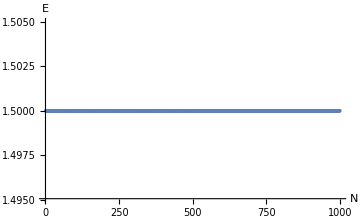

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
ReadList["dataE.txt"];
ListPlot[%,AxesLabel->{"N","E"},PlotRange->{1.495,1.505},ImageSize->Medium]
```

Όπως φαίνεται και από το παραπάνω διάγραμμα (βασισμένο στην τιμή της ενέργειας μετά από κάθε βήμα της μεθόδου) η μέθοδος διατηρεί την ενέργεια στα επιθυμιτά επίπεδα.